14.7 HW # 27

```mathematica
f[x_,y_]=x^4+y^3-3 x^2+y^2+x-2y+1;
fx[x_,y_]=D[f[x,y],x];
fy[x_,y_]=D[f[x,y],y];
```

```mathematica
Solve[fx[x,y]==0&&fy[x,y]==0,{x,y},Reals]//N
```

{{x→-1.30084,y→-1.21525},{x→-1.30084,y→0.548584},{x→0.169938,y→-1.21525},{x→0.169938,y→0.548584},{x→1.1309,y→-1.21525},{x→1.1309,y→0.548584}}

-Graphics3D-

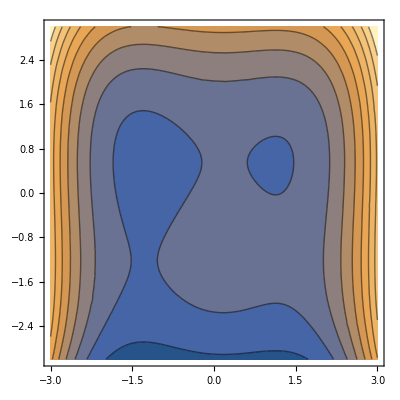

```mathematica
ContourPlot3D[z==f[x,y],{x,-2,2},{y,-2,2},{z,-2,2}]
ContourPlot[f[x,y], {x,-3,3},{y,-3,3},Contours->10]
```